```mathematica
ClearAll@bsa;
basicFunction[k_]:=(#^(k/2))&;
bsa[func_,left_,right_,k_]:=Module[{ϕ,a,f,c},
ϕ=Table[basicFunction[i-1],{i,k}];
c=Table[
NIntegrate[ϕ[[i]][x]*ϕ[[j]][x],{x,left,right}]
,{i,k},{j,k}];
f=Table[
NIntegrate[ϕ[[i]][x]*func[x],{x,left,right}]
,{i,k}];
a=LinearSolve[c,f];
Sum[a[[i]]ϕ[[i]][#],{i,k}]&
]
show[]:=Module[
{
f,h, x0=0, x1=10
},
f[x_]:=Log[E^x+0.01](Sin[80x]+x);
h=bsa[f,x0,x1,4];
Show[
Plot[f[x],{x,x0,x1}],
Plot[h[x],{x,x0,x1},PlotStyle->Black]
]
]
```

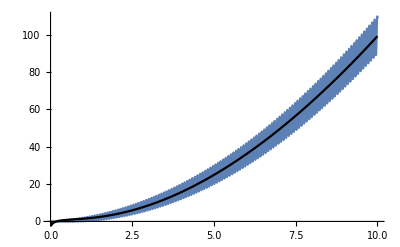

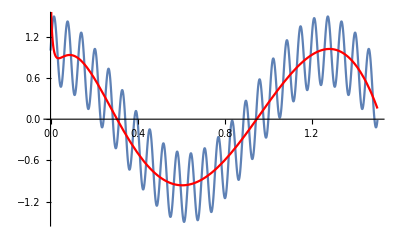

```mathematica
show[]
```

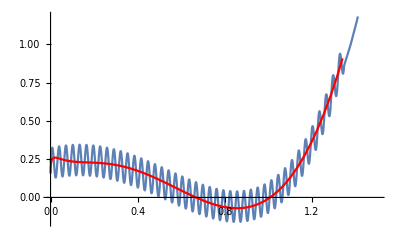

```mathematica
f2[x_]:=(x-1)(x+1)(x-2/3)(x+1/3)+0.1Sin[200x];
res2=bsa[f2,0,1.5,6];
Show[
Plot[f2[x],{x,0,1.5}],
Plot[res2[x],{x,0,1.5},PlotStyle->Red]
]
```

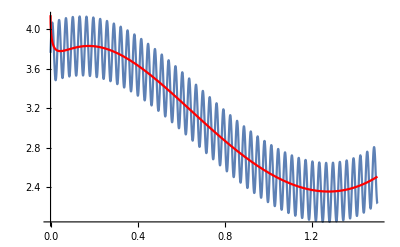

```mathematica
f3[x_]:=Cosh[-x^2+2]+x+0.3Sin[200x];
res3=bsa[f3,0,1.5,5];
Show[
Plot[f3[x],{x,0,1.5}],
Plot[res3[x],{x,0,1.5},PlotStyle->Red]
]
```

```mathematica
f1[x_]:=Cos[5x]+0.5Sin[200x];
f2[x_]:=(x-1)(x+1)(x-2/3)(x+1/3)+0.1Sin[200x];
f3[x_]:=Cosh[-x^2+1]+x+0.2Sin[200x];
```